This notebook contains symbolic calculations for estimation of a squeezing parameter encoded in the mean and/or covariances of a Gaussian state. 

Last updated: 06/03/26.

## Quadratic 𝒮 for squeezing

### Zero mean

Use the quadratic centred basis B={1,Δx^2,Δp^2} with Δx^2=(x̂)^2-Tr(ρ_0(x̂)^2) and Δp^2=(p̂)^2-Tr(ρ_0(p̂)^2)

```mathematica
(*Choose a Gaussian prior for simple moments*)
p[θ_]:=PDF[NormalDistribution[μ0,σ0],θ];

(*Subscript[ρ, 0] averages*)
avgx2ρ0=Integrate[Vxx Exp[-2 θ] p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]
avgp2ρ0=Integrate[Vpp Exp[2 θ] p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]

avgx4ρ0=Integrate[3 (Vxx Exp[-2 θ])^2 p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]
avgp4ρ0=Integrate[3 (Vpp Exp[2 θ])^2 p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]
avgx2p2ρ0=Integrate[(Vxx Vpp-1/2) p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]
(*Centered Gram elements*)
Gxx=avgx4ρ0-avgx2ρ0^2;
Gpp=avgp4ρ0-avgp2ρ0^2;
Gxp=avgx2p2ρ0-avgx2ρ0*avgp2ρ0;
(*Build quadratic block*)
M={{Gxx,Gxp},{Gxp,Gpp}}//FullSimplify;
M//MatrixForm
```

ⅇ^(-2 μ0+2 σ0^2) Vxx

ⅇ^(2 (μ0+σ0^2)) Vpp

3 ⅇ^(-4 μ0+8 σ0^2) Vxx^2

3 ⅇ^(4 μ0+8 σ0^2) Vpp^2

-1/2+Vpp Vxx

(ⅇ^(-4 μ0+4 σ0^2) (-1+3 ⅇ^(4 σ0^2)) Vxx^2 | -1/2-(-1+ⅇ^(4 σ0^2)) Vpp Vxx
-1/2-(-1+ⅇ^(4 σ0^2)) Vpp Vxx | ⅇ^(4 (μ0+σ0^2)) (-1+3 ⅇ^(4 σ0^2)) Vpp^2)

b_i=Tr(ρ̄ B_i)

```mathematica
(*b vector*)
bx=Integrate[θ Vxx Exp[-2 θ] p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]-μ0*avgx2ρ0//Simplify
bp=Integrate[θ Vpp Exp[2 θ] p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]-μ0*avgp2ρ0 // Simplify
b={bx,bp};
(*Solve*)
alpha=Simplify[Inverse[M].b]
(*Small sigma expansion*)
alphaSeries=Normal[Series[alpha,{σ0,0,2}]]
```

-2 ⅇ^(-2 μ0+2 σ0^2) Vxx σ0^2

2 ⅇ^(2 (μ0+σ0^2)) Vpp σ0^2

{-(4 ⅇ^(2 (μ0+σ0^2)) Vpp σ0^2)/(1+2 (-1+3 ⅇ^(8 σ0^2)) Vpp Vxx),(4 ⅇ^(-2 μ0+2 σ0^2) Vxx σ0^2)/(1+2 (-1+3 ⅇ^(8 σ0^2)) Vpp Vxx)}

{-(4 ⅇ^(2 μ0) Vpp σ0^2)/(1+4 Vpp Vxx),(4 ⅇ^(-2 μ0) Vxx σ0^2)/(1+4 Vpp Vxx)}

```mathematica
alpha[[2]]/alpha[[1]]//Simplify

alphaSeries[[2]]/alphaSeries[[1]]//Simplify
```

-(ⅇ^(-4 μ0) Vxx)/Vpp

-(ⅇ^(-4 μ0) Vxx)/Vpp

```mathematica
(* Now calculate the constrained MSL ℒ(Subscript[𝒮, 𝒱])=λ-b^T G^-1 b *)

λ=Integrate[θ^2 p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]  

MSL=λ-b.Inverse[M].b//Simplify
```

μ0^2+σ0^2

μ0^2+(σ0^2 (1+2 Vpp Vxx (-1+3 ⅇ^(8 σ0^2)-8 ⅇ^(4 σ0^2) σ0^2)))/(1+2 (-1+3 ⅇ^(8 σ0^2)) Vpp Vxx)

```mathematica
μ0^2+(σ0^2 (1+2 Vpp Vxx (-1+3 ⅇ^(8 σ0^2)-8 ⅇ^(4 σ0^2) σ0^2)))/(1+2 (-1+3 ⅇ^(8 σ0^2)) Vpp Vxx)//FullSimplify
```

μ0^2+σ0^2-(16 ⅇ^(4 σ0^2) Vpp Vxx σ0^4)/(1-2 Vpp Vxx+6 ⅇ^(8 σ0^2) Vpp Vxx)

```mathematica
Normal[Series[MSL,{σ0,0,4}]]
```

μ0^2+σ0^2-(16 Vpp Vxx σ0^4)/(1+4 Vpp Vxx)

### Non-zero mean

Use the linear basis B={1,Δx,Δp} where Δx=x̂-Tr(ρ_0 x̂) and similarly for p.

```mathematica
p[θ_]:=PDF[NormalDistribution[μ0,σ0],θ];
(*First moments*)
avgxρ0=Integrate[μx Exp[- θ] p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]
avgpρ0=Integrate[μp Exp[ θ] p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]

(*Second moments*)
avgx2ρ0=Integrate[(Vxx+μx^2) Exp[-2 θ] p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]
avgp2ρ0=Integrate[(Vpp+μp^2) Exp[2 θ] p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]
(*Mixed moment*)
avgxpρ0=Integrate[μx μp p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]
(*Centered Gram elements*)
Gxx=avgx2ρ0-avgxρ0^2;
Gpp=avgp2ρ0-avgpρ0^2;
Gxp=avgxpρ0-avgxρ0*avgpρ0;
(*Build quadratic block*)
M={{Gxx,Gxp},{Gxp,Gpp}}//FullSimplify;
M//MatrixForm
```

ⅇ^(-μ0+σ0^2/2) μx

ⅇ^(μ0+σ0^2/2) μp

ⅇ^(-2 μ0+2 σ0^2) (Vxx+μx^2)

ⅇ^(2 (μ0+σ0^2)) (Vpp+μp^2)

μp μx

(ⅇ^(-2 μ0+σ0^2) (-μx^2+ⅇ^(σ0^2) (Vxx+μx^2)) | -((-1+ⅇ^(σ0^2)) μp μx)
-((-1+ⅇ^(σ0^2)) μp μx) | ⅇ^(2 μ0+σ0^2) (-μp^2+ⅇ^(σ0^2) (Vpp+μp^2)))

```mathematica
(*b vector*)
bx=Integrate[θ μx Exp[- θ] p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]-μ0*avgxρ0//Simplify
bp=Integrate[θ μp Exp[ θ] p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]-μ0*avgpρ0 // Simplify
b={bx,bp};
(*Solve*)
alpha=Simplify[Inverse[M].b]//FullSimplify
(*Small sigma expansion*)
alphaSeries=Normal[Series[alpha,{σ0,0,2}]]//FullSimplify
```

-ⅇ^(-μ0+σ0^2/2) μx σ0^2

ⅇ^(μ0+σ0^2/2) μp σ0^2

{-(ⅇ^(μ0+σ0^2/2) (μp^2-2 ⅇ^(σ0^2) μp^2+ⅇ^(2 σ0^2) (Vpp+μp^2)) μx σ0^2)/(-μp^2 μx^2+2 ⅇ^(σ0^2) μp^2 μx^2+ⅇ^(4 σ0^2) (Vpp+μp^2) (Vxx+μx^2)-ⅇ^(3 σ0^2) (Vxx μp^2+(Vpp+2 μp^2) μx^2)),(ⅇ^(-μ0+σ0^2/2) μp (μx^2-2 ⅇ^(σ0^2) μx^2+ⅇ^(2 σ0^2) (Vxx+μx^2)) σ0^2)/(-μp^2 μx^2+2 ⅇ^(σ0^2) μp^2 μx^2+ⅇ^(4 σ0^2) (Vpp+μp^2) (Vxx+μx^2)-ⅇ^(3 σ0^2) (Vxx μp^2+(Vpp+2 μp^2) μx^2))}

{-(ⅇ^μ0 μx σ0^2)/Vxx,(ⅇ^-μ0 μp σ0^2)/Vpp}

```mathematica
alpha[[2]]/alpha[[1]]//FullSimplify
```

-(ⅇ^(-2 μ0) μp (μx^2-2 ⅇ^(σ0^2) μx^2+ⅇ^(2 σ0^2) (Vxx+μx^2)))/((μp^2-2 ⅇ^(σ0^2) μp^2+ⅇ^(2 σ0^2) (Vpp+μp^2)) μx)

```mathematica
alphaSeries[[2]]/alphaSeries[[1]]//Simplify
```

-(ⅇ^(-2 μ0) Vxx μp)/(Vpp μx)

```mathematica
Series[alpha[[2]]/alpha[[1]],{σ0,0,4}]
```

-(ⅇ^(-2 μ0) Vxx μp)/(Vpp μx)-(ⅇ^(-2 μ0) μp (-Vxx μp^2+Vpp μx^2) σ0^4)/(Vpp^2 μx)+O[σ0]^5

```mathematica
(* Now calculate the constrained MSL ℒ(Subscript[𝒮, 𝒱])=λ-b^T G^-1 b *)

λ=Integrate[θ^2 p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]  

MSL=λ-b.Inverse[M].b//FullSimplify
```

μ0^2+σ0^2

μ0^2+σ0^2+(ⅇ^(σ0^2) (-2 μp^2 μx^2+4 ⅇ^(σ0^2) μp^2 μx^2-ⅇ^(2 σ0^2) (Vxx μp^2+(Vpp+2 μp^2) μx^2)) σ0^4)/(-μp^2 μx^2+2 ⅇ^(σ0^2) μp^2 μx^2+ⅇ^(4 σ0^2) (Vpp+μp^2) (Vxx+μx^2)-ⅇ^(3 σ0^2) (Vxx μp^2+(Vpp+2 μp^2) μx^2))

```mathematica
(*MSL for a squeeed displaced probe*)

Normal[Series[MSL/.{Vxx->Exp[2r],Vpp->Exp[-2r],μx->μ*Cos[ϕ],μp->μ*Sin[ϕ]},{σ0,0,4}]]//FullSimplify
```

μ0^2+σ0^2-ⅇ^(-2 r) μ^2 σ0^4 (Cos[ϕ]^2+ⅇ^(4 r) Sin[ϕ]^2)

```mathematica
Mod[(ϕ/.Maximize[{ⅇ^(-2 r) (Cos[ϕ]^2+ⅇ^(4 r) Sin[ϕ]^2)/.{r->12},0<=ϕ<2π},ϕ][[2,1]]) ,π](*MSL Maximised at ϕ=π/2+kπ*)
```

π/2

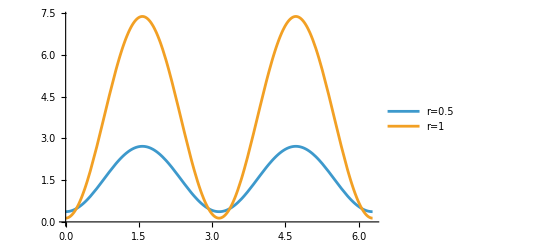

```mathematica
Plot[Evaluate@Table[ⅇ^(-2 r) (Cos[ϕ]^2+ⅇ^(4 r) Sin[ϕ]^2),{r,{0.5,1}}],{ϕ,0,2π},PlotLegends->Table[StringForm["r=``",r],{r,{0.5,1}}]]
```

```mathematica
InfoGainSqueezedDisplaced[μ0_,σ0_,μ_,ϕ_,r_]=λ-MSL/.{Vxx->Exp[2r],Vpp->Exp[-2r],μx->μ*Cos[ϕ],μp->μ*Sin[ϕ]}//Simplify
```

(ⅇ^(σ0^2) μ^2 σ0^4 (ⅇ^(4 r+2 σ0^2) Sin[ϕ]^2+Cos[ϕ]^2 (ⅇ^(2 σ0^2)+2 ⅇ^(2 r) (-1+ⅇ^(σ0^2))^2 μ^2 Sin[ϕ]^2)))/(ⅇ^(2 r+3 σ0^2) (ⅇ^(σ0^2)+ⅇ^(2 r) (-1+ⅇ^(σ0^2)) μ^2 Sin[ϕ]^2)+(-1+ⅇ^(σ0^2)) μ^2 Cos[ϕ]^2 (ⅇ^(3 σ0^2)+ⅇ^(2 r) (-1+ⅇ^(σ0^2))^2 (1+ⅇ^(σ0^2)) μ^2 Sin[ϕ]^2))

```mathematica
Mod[ϕ/.FindMaximum[{InfoGainSqueezedDisplaced[1,1,1,ϕ,1],0<=ϕ<2π},ϕ][[2,1]],π]
```

1.5708

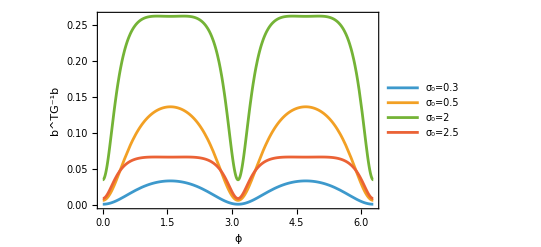

```mathematica
σ0list={0.3,0.5,2,2.5};

Plot[Evaluate@Table[InfoGainSqueezedDisplaced[1,σ0,1,ϕ,1],{σ0,σ0list}],{ϕ,0,2π},PlotLegends->Table[StringForm["σ_0=``",σ0],{σ0,σ0list}],Frame->True,FrameLabel->{"ϕ","b^TG^-1b"}]

(*σ0list={3,3.5,4};

Plot[Evaluate@Table[InfoGainSqueezedDisplaced[1,σ0,1,ϕ,1],{σ0,σ0list}],{ϕ,0,2π},PlotLegends->Table[StringForm["σ_0=``",σ0],{σ0,σ0list}],Frame->True,FrameLabel->{"ϕ","b^TG^-1b"}]*)
```

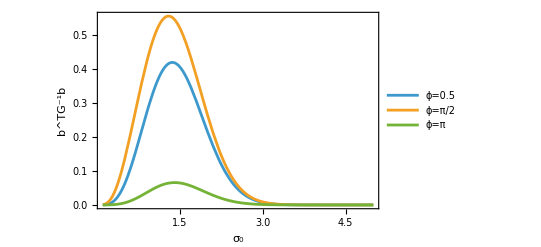

```mathematica
Plot[Evaluate@Table[InfoGainSqueezedDisplaced[1,σ0,1,ϕ,1],{ϕ,{0.5,π/2,π}}],{σ0,0.1,5},PlotLegends->Table[StringForm["ϕ=``",ϕ],{ϕ,{0.5,π/2,π}}],Frame->True,FrameLabel->{"σ_0","b^TG^-1b"},PlotRange->All]
```

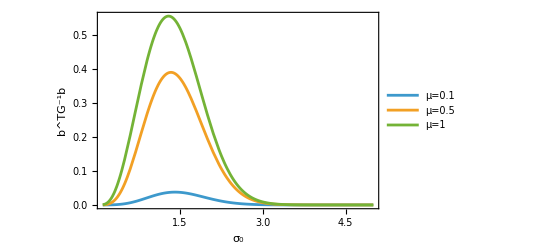

```mathematica
Plot[Evaluate@Table[InfoGainSqueezedDisplaced[1,σ0,μ,π/2,1],{μ,{0.1,0.5,1}}],{σ0,0.1,5},PlotLegends->Table[StringForm["μ=``",μ],{μ,{0.1,0.5,1}}],Frame->True,FrameLabel->{"σ_0","b^TG^-1b"},PlotRange->All]
```

### Symmetric logarithmic derivative (SLD)

We want to obtain the symmetric logarithmic derivative. For a Gaussian state, it is a quadratic form of position and momentum (x and p) 

ℒ=∑_ij L_ij 1/2{R_i-d_i,R_j-d_j}_++∑_i b_i(R_i-d_i)-1/2 tr{L Γ},

here, d_i=⟨R_i⟩=tr{R_i ρ}, R⃗=(x,p), Γ=2σ and σ_ij=1/2⟨{R_i,R_j}_+⟩ are the elements of the (symmetrized) covariance matrix. See Monras (2013) https://arxiv.org/pdf/1303.3682.

Here, Ω=(0 | -1
1 | 0) is the symplectic matrix. 

The coefficients are given by

L=𝒟_Γ^-1(∂Γ)
b⃗=2 Γ^-1∂d⃗,

where the application 𝒟_Γ(Y)=Γ Y Γ^T-Ω Y Ω^T, and ∂ is a shorthand for ∂/∂θ. Hence, 𝒟_Γ^-1(∂Γ) is the solution Y to the matrix equation

∂Γ=Γ Y Γ^T-Ω Y Ω^T
Ω^-1∂Γ (Ω^T)^-1=Ω^-1 Γ Y (Γ^T(Ω^T))^-1-Y
Ω^T∂Γ Ω=(Ω^T Γ)(Y(Ω^T Γ))^T-Y
Y-F Y F^T=-Ω^T∂Γ Ω.

In our case, we have

```mathematica
covSqueezed[θ_]:=({{Vxx*Exp[-2θ], 0}, {0, Vpp*Exp[2θ]}})
```

```mathematica
mL=({{L[1,1], L[1,2]}, {L[2,1], L[2,2]}});
Γ=2covSqueezed[θ];
dΓ=D[2covSqueezed[θ],θ]//FullSimplify;
Ω=({{0, -1}, {1, 0}});
F=Transpose[Ω].Γ;
```

```mathematica
sol=Solve[Flatten[mL-F.mL.Transpose[F]]⟦#⟧==Flatten[-Transpose[Ω].dΓ.Ω]⟦#⟧&/@Range[4],Flatten[mL]]//FullSimplify;mL/.Flatten[sol]//MatrixForm//TraditionalForm
```

(-(4 ⅇ^(2 θ) Vpp)/(4 Vpp Vxx+1) | 0
0 | (4 ⅇ^(-2 θ) Vxx)/(4 Vpp Vxx+1))

Note that Y-F Y F^T=-Ω^T∂Γ Ω is a discrete-time Lyapunov equation, whose solution is formally given by Y = -∑_k F^k(Ω^T∂Γ Ω)F^(T k).

```mathematica
-Sum[FullSimplify[MatrixPower[F,k].Transpose[Ω].dΓ.Ω.MatrixPower[Transpose[F],k],Assumptions->{k∈Integers,k>0}],{k,0,Infinity}]//MatrixForm//TraditionalForm
```

(-(4 ⅇ^(2 θ) Vpp)/(4 Vpp Vxx+1) | 0
0 | (4 ⅇ^(-2 θ) Vxx)/(4 Vpp Vxx+1))

The linear term b⃗=2 Γ^-1∂d⃗ is

```mathematica
Inverse[Γ].D[2{x0*Exp[-θ],p0*Exp[θ]},θ]//FullSimplify
```

{-(ⅇ^θ x0)/Vxx,(ⅇ^-θ p0)/Vpp}

The constant term is -1/2tr{L Γ}=0 in our case

```mathematica
-1/2 Tr[(mL/.Flatten[sol]).Γ]
```

0

```mathematica
(* The QFI *)
1/2(mL/.Flatten[sol]).dΓ//Diagonal//Total
```

(16 Vpp Vxx)/(1+4 Vpp Vxx)

```mathematica
(*This matches the MSL of for the quadratic basis {1,Δx^2,Δp^2}*)
Normal[Series[MSL,{σ0,0,4}]]
```

μ0^2+σ0^2-(16 Vpp Vxx σ0^4)/(1+4 Vpp Vxx)